```mathematica
2-2
```

0

```mathematica
Adjoint[x_]:=Transpose[Conjugate[x]]
```

```mathematica
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
```

# Quantum Walks on Graphs

Nicholas Wheeler
30 October 2011

### Introduction

Matthew Jemielita (October 2008) announced to me—his designated thesis advisor—that he proposed to explore aspects of the quantum theory of random walks. I was, at that time, only dimly aware that such a topic even existed; I had studied none of the literature, and had no idea why that subject was of interest, and certainly not of why it had recently acquired urgent interest, though I was aware that it had engaged the attention of two applicants (Andrew Childs and Cesar Rodriguez-Rosario) for positions on the Reed College physics faculty.

I return to the subject now because it involves many of the ideas and methods that play roles in the subject of primary interest to me at the moment—the quantum theory of open systems, to which the quantum theory of walks provides a kind of introduction.

The literature in these areas has become immense (ask Google). Basic references can be found in Matt's bibliography: "Quantum Walks on Graphs," Reed College thesis (2009). I, however, will be content to follow my own nose, drawing upon and citing literature only when it bears upon a specific problem or issue, serves a specific need.

### Representatives of quantum state

#### State vectors

The state of a quantum walker on a finite graph can, in the simplest instance, be described by a "complex stochastic vector"—a complex vector (dimension = number of graph nodes) with unit norm. Individual elements of such a state vector are "probability amplitudes."

I look to some of the commands that bear on the construction  and manipulation of such objects. My immediate purpose will be to identify certain quirks of Mathematica's command structure, and to devise work-arounds. 

I assume arbitrarily that we are concerned with quantum walks on 5-node graphs.

The commands Normalize and Norm operate on simple lists, not on column/row vectors: thus

```mathematica
RandomComplex[{},5]
```

{0.051769+0.617686 ⅈ,0.689188+0.925342 ⅈ,0.208051+0.600421 ⅈ,0.907079+0.52165 ⅈ,0.667587+0.513975 ⅈ}

```mathematica
Norm[%]
Normalize[%%]
Norm[%]
```

1.98091

{0.0261339+0.31182 ⅈ,0.347915+0.46713 ⅈ,0.105028+0.303104 ⅈ,0.457911+0.263339 ⅈ,0.337011+0.259464 ⅈ}

1.

We will have interest most commonly in column vectors, which are easy to construct

```mathematica
RandomComplex[{},{5,1}]//MatrixForm
```

(0.673402+0.172979 ⅈ
0.0681456+0.562152 ⅈ
0.889828+0.0175595 ⅈ
0.78285+0.780597 ⅈ
0.532665+0.404888 ⅈ)

but not so easy to process. It is always best, therefore, to work from row vectors from which the outer braces have been removed

```mathematica
RandomComplex[{},{1,5}]
%⟦1⟧
```

{{0.553576+0.552449 ⅈ,0.817901+0.923001 ⅈ,0.64682+0.0921497 ⅈ,0.794339+0.842711 ⅈ,0.959587+0.0627496 ⅈ}}

{0.553576+0.552449 ⅈ,0.817901+0.923001 ⅈ,0.64682+0.0921497 ⅈ,0.794339+0.842711 ⅈ,0.959587+0.0627496 ⅈ}

or—more simply—to start from lists, and to look upon state vectors and their adjoints as assembled objects. Thus

```mathematica
Subscript[ψ, row]={Normalize[RandomComplex[{},5]]}
```

{{0.418425+0.441438 ⅈ,0.430966+0.135977 ⅈ,0.00454828+0.372148 ⅈ,0.31631+0.0996268 ⅈ,0.024828+0.420384 ⅈ}}

```mathematica
Norm[Subscript[ψ, row]⟦1⟧]
```

1.

and

```mathematica
Subscript[ψ, column]=Transpose[Subscript[ψ, row]]
```

{{0.418425+0.441438 ⅈ},{0.430966+0.135977 ⅈ},{0.00454828+0.372148 ⅈ},{0.31631+0.0996268 ⅈ},{0.024828+0.420384 ⅈ}}

```mathematica
Subscript[ψ, column]//MatrixForm
```

(0.418425+0.441438 ⅈ
0.430966+0.135977 ⅈ
0.00454828+0.372148 ⅈ
0.31631+0.0996268 ⅈ
0.024828+0.420384 ⅈ)

The following commands distribute over lists of lists provided they are not presented in MatrixForm:

```mathematica
Conjugate[Subscript[ψ, column]]
Re[Subscript[ψ, column]]
Im[Subscript[ψ, column]]
Abs[Subscript[ψ, column]]
Arg[Subscript[ψ, column]]
```

{{0.418425-0.441438 ⅈ},{0.430966-0.135977 ⅈ},{0.00454828-0.372148 ⅈ},{0.31631-0.0996268 ⅈ},{0.024828-0.420384 ⅈ}}

{{0.418425},{0.430966},{0.00454828},{0.31631},{0.024828}}

{{0.441438},{0.135977},{0.372148},{0.0996268},{0.420384}}

{{0.608233},{0.451909},{0.372176},{0.331629},{0.421116}}

{{0.812156},{0.305632},{1.55858},{0.305129},{1.5118}}

The adjoint of a rectangular matrix is produced by the command

```mathematica
Adjoint[x_]:=Transpose[Conjugate[x]]
```

Thus

```mathematica
Subscript[ψ, column]
Adjoint[Subscript[ψ, column]]
```

{{0.418425+0.441438 ⅈ},{0.430966+0.135977 ⅈ},{0.00454828+0.372148 ⅈ},{0.31631+0.0996268 ⅈ},{0.024828+0.420384 ⅈ}}

{{0.418425-0.441438 ⅈ,0.430966-0.135977 ⅈ,0.00454828-0.372148 ⅈ,0.31631-0.0996268 ⅈ,0.024828-0.420384 ⅈ}}

Observe that

```mathematica
Adjoint[Adjoint[Subscript[ψ, column]]]==Subscript[ψ, column]
Adjoint[Adjoint[Subscript[ψ, row]]]==Subscript[ψ, row]
```

True

True

and that in confirmation of the normalization of ψ_column we have

```mathematica
Chop[Adjoint[Subscript[ψ, column]].Subscript[ψ, column]]⟦1⟧⟦1⟧
```

1.

Probabilities arise in quantum theory as the squared modulii of probability amplitudes, and can be looked upon as elements of a stochastic vector in the classical sense:

```mathematica
Table[Subscript[P, k]=Abs[Subscript[ψ, column]⟦k⟧⟦1⟧]^2,{k,1,5}]
```

{0.369947,0.204221,0.138515,0.109978,0.177339}

```mathematica
Total[%]
```

1.

#### Density matrices

The matrix

```mathematica
Subscript[ℙ, ψ]=Subscript[ψ, column].Adjoint[Subscript[ψ, column]]//Chop;
Subscript[ℙ, ψ]//MatrixForm
```

(0.369947 | 0.240352+0.133348 ⅈ | 0.166184-0.153708 ⅈ | 0.176331+0.0979451 ⅈ | 0.195962-0.164939 ⅈ
0.240352-0.133348 ⅈ | 0.204221 | 0.0525639-0.159765 ⅈ | 0.149866+0.0000752634 ⅈ | 0.0678627-0.177795 ⅈ
0.166184+0.153708 ⅈ | 0.0525639+0.159765 ⅈ | 0.138515 | 0.0385146+0.117261 ⅈ | 0.156558+0.00732767 ⅈ
0.176331-0.0979451 ⅈ | 0.149866-0.0000752634 ⅈ | 0.0385146-0.117261 ⅈ | 0.109978 | 0.0497349-0.130498 ⅈ
0.195962+0.164939 ⅈ | 0.0678627+0.177795 ⅈ | 0.156558-0.00732767 ⅈ | 0.0497349+0.130498 ⅈ | 0.177339)

is manifestly hermitian (self-adjoint)

```mathematica
Chop[Adjoint[Subscript[ℙ, ψ]]-Subscript[ℙ, ψ]]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

has unit trace

```mathematica
Tr[Subscript[ℙ, ψ]]
```

1.

and is projective:

```mathematica
Chop[Subscript[ℙ, ψ].Subscript[ℙ, ψ]-Subscript[ℙ, ψ]]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

It is seen from

```mathematica
Eigenvalues[Subscript[ℙ, ψ]]//Chop
```

{1.,0,0,0,0}

to project onto a one-space, which is in fact the one-space spanned by ψ_column:

```mathematica
Subscript[ℙ, ψ].Subscript[ψ, column]==Subscript[ψ, column]
```

True

ℙ_ψ is a "pure state" density matrix. The density matrix concept (due originally to von Neumann and—inxependently—Weyl) derives its importance from the fact that it permits one to describe mixtures of quantum states ("impure states," or simply "mixtures," "mixed states"). To undertake construction of such a generalized density matrix…

…Construct at random a set of (let us say) 3 state vectors

```mathematica
Table[Subscript[ψ, k]=Transpose[{Normalize[RandomComplex[{},5]]}],{k,1,3}];
```

and assemble the associated projection matrices

```mathematica
Table[Subscript[ℙ, k]=Chop[Subscript[ψ, k].Adjoint[Subscript[ψ, k]]],{k,1,3}];
```

Construct at random a 3-element classical stochastic vector (stochastic vector with real elements)

```mathematica
q=RandomReal[{},3];
Q=q/Total[q];
Table[Subscript[p, k]=Q⟦k⟧,{k,1,3}];
Table[Subscript[p, k],{k,1,3}]
Total[%]
```

{0.368535,0.601639,0.0298266}

1.

and finally assemble the generalized density matrix

```mathematica
ρ=∑_(k=1)^3 Subscript[p, k] Subscript[ℙ, k];
ρ//MatrixForm
```

(0.18977 | 0.179867+0.00277192 ⅈ | 0.231845-0.140618 ⅈ | 0.0729525-0.0260224 ⅈ | 0.0584605-0.0903052 ⅈ
0.179867-0.00277192 ⅈ | 0.216494 | 0.257433-0.141869 ⅈ | 0.111432-0.0124316 ⅈ | 0.0682564-0.107209 ⅈ
0.231845+0.140618 ⅈ | 0.257433+0.141869 ⅈ | 0.431077 | 0.150443+0.0371741 ⅈ | 0.160195-0.0869372 ⅈ
0.0729525+0.0260224 ⅈ | 0.111432+0.0124316 ⅈ | 0.150443-0.0371741 ⅈ | 0.0803861 | 0.0481445-0.0516289 ⅈ
0.0584605+0.0903052 ⅈ | 0.0682564+0.107209 ⅈ | 0.160195+0.0869372 ⅈ | 0.0481445+0.0516289 ⅈ | 0.082273)

ρ is manifestly hermitian and has unit trace

```mathematica
Tr[ρ]
```

1.

but is on the following evidence

```mathematica
Eigenvalues[ρ]//Chop
```

{0.9384,0.0536823,0.00791816,0,0}

clearly NOT projective. It descibes a "mixed state" of the quantum system—a circumstance usually typified

```mathematica
Chop[Tr[ρ.ρ]]<Tr[ρ]==1
```

True

I describe now a more efficient way to construct random density matrices.

The following "supersymmetric construction" is easily seen to result in hermitian matrices with non-negative spectra (such as density matrices are required to possess):

```mathematica
𝕞=RandomComplex[{},{5,5}];
𝕤=Chop[𝕞.Adjoint[𝕞]]
```

{{2.21889,2.26486-0.644814 ⅈ,2.1387-0.01218 ⅈ,1.79101-0.177534 ⅈ,1.88226+0.11757 ⅈ},{2.26486+0.644814 ⅈ,3.83023,3.10842+1.42473 ⅈ,2.76236+0.0536364 ⅈ,3.4196+0.976171 ⅈ},{2.1387+0.01218 ⅈ,3.10842-1.42473 ⅈ,3.81909,2.23561-0.97509 ⅈ,2.92793-0.529656 ⅈ},{1.79101+0.177534 ⅈ,2.76236-0.0536364 ⅈ,2.23561+0.97509 ⅈ,2.47241,2.73309+0.92553 ⅈ},{1.88226-0.11757 ⅈ,3.4196-0.976171 ⅈ,2.92793+0.529656 ⅈ,2.73309-0.92553 ⅈ,3.99694}}

We have at this point only to adjust the trace

```mathematica
𝕣=𝕤/Tr[𝕤];
𝕣//MatrixForm
```

(0.135815 | 0.138629-0.0394682 ⅈ | 0.130907-0.000745523 ⅈ | 0.109625-0.0108666 ⅈ | 0.11521+0.00719633 ⅈ
0.138629+0.0394682 ⅈ | 0.234443 | 0.190262+0.0872058 ⅈ | 0.16908+0.00328301 ⅈ | 0.209309+0.0597501 ⅈ
0.130907+0.000745523 ⅈ | 0.190262-0.0872058 ⅈ | 0.233761 | 0.136839-0.0596839 ⅈ | 0.179214-0.0324195 ⅈ
0.109625+0.0108666 ⅈ | 0.16908-0.00328301 ⅈ | 0.136839+0.0596839 ⅈ | 0.151333 | 0.167289+0.0566505 ⅈ
0.11521-0.00719633 ⅈ | 0.209309-0.0597501 ⅈ | 0.179214+0.0324195 ⅈ | 0.167289-0.0566505 ⅈ | 0.244648)

```mathematica
Tr[𝕣]
```

1.

to obtain a random instance of a density matrix. Note that the eigenvalues

```mathematica
Eigenvalues[𝕣]//Chop
```

{0.860893,0.0892681,0.03386,0.0127341,0.00324511}

are non-negative, and sum to unity:

```mathematica
Total[%]
```

1.

Though spectral evidence serves already to establish the point, the impurity of 𝕣 is most economically formulated

```mathematica
Chop[Tr[𝕣.𝕣]]<Tr[𝕣]==1
```

True

I look next to the spectral decomposition of the density matrix 𝕣.

```mathematica
Table[Subscript[e, k]=Transpose[{Chop[Eigenvectors[𝕣]⟦k⟧]}],{k,1,5}];

Table[MatrixForm[Subscript[e, k]],{k,1,5}]
```

{(0.313328-0.0882718 ⅈ
0.513488
0.435544-0.193869 ⅈ
0.395873-0.00743353 ⅈ
0.475599-0.141826 ⅈ),(0.603915
-0.019485+0.0349148 ⅈ
0.164108+0.488982 ⅈ
0.0312075-0.323488 ⅈ
-0.437883-0.265128 ⅈ),(-0.48544+0.291842 ⅈ
-0.105012+0.047288 ⅈ
0.64054
0.01252+0.107423 ⅈ
-0.237168-0.433215 ⅈ),(-0.0502506+0.222252 ⅈ
0.690066
-0.104185+0.0629669 ⅈ
-0.664344-0.0144089 ⅈ
-0.0326879-0.120164 ⅈ),(-0.373175-0.131589 ⅈ
0.493771-0.0382924 ⅈ
-0.182147+0.219981 ⅈ
0.533249
-0.441394+0.193382 ⅈ)}

These vectors are orthogonal, and (as supplied by Mathematica) already normalized:

```mathematica
Table[Chop[Adjoint[Subscript[e, i]].Subscript[e, j]]⟦1⟧⟦1⟧,{i,1,5},{j,1,5}]//TableForm
```

1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.

Introducing the associated projectors

```mathematica
Table[Subscript[𝔼, k]=Chop[Subscript[e, k].Adjoint[Subscript[e, k]]],{k,1,5}];
```

(these are easily demonstrated to comprise a complete set of orthogonal projection matrices) we give names to the eigenvalues of 𝕣

```mathematica
Table[Subscript[λ, k]=Chop[Eigenvalues[𝕣]⟦k⟧],{k,1,5}]
```

{0.860893,0.0892681,0.03386,0.0127341,0.00324511}

and have

```mathematica
Chop[𝕣-∑_(k=1)^5 Subscript[λ, k] Subscript[𝔼, k]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

which displays 𝕣 as a λ-weighted mixture of eigenstates. 

Generally, indefinitely many distinct mixtures can result in the same density matrix, meaning that in quantum mechanics there is—in contradistinction to all classical uses of the term "mixture," and except for pure states—no unique response to the question "Mixture of WHAT?" The "spectral" response to that question, developed above, occupies a distinguished place in the mathematics of this subject, but not in its physics.

### General quantum dynamics on graphs

The quantum mechanics of systems with finite-dimensional state vectors is structurally identical to quantum-mechanics-in-general, except that it is deprived of the fundamental relation

𝕩.𝕡-𝕡.𝕩=ⅈ ℏ 𝕀

and all of its consequences.

Most simply, one specifies a hermitian Hamiltonian matrix

```mathematica
𝕙=RandomComplex[{},{5,5}];
ℍ=Chop[𝕙.Adjoint[𝕙]];
ℍ//MatrixForm
```

(3.89923 | 4.13389-0.642677 ⅈ | 3.15479-0.774021 ⅈ | 2.64682+0.0918986 ⅈ | 2.31364+0.079418 ⅈ
4.13389+0.642677 ⅈ | 5.69981 | 3.78606+0.0500096 ⅈ | 3.04952+0.15271 ⅈ | 2.82847+1.10626 ⅈ
3.15479+0.774021 ⅈ | 3.78606-0.0500096 ⅈ | 3.21438 | 1.81057+0.507678 ⅈ | 2.14334+0.617745 ⅈ
2.64682-0.0918986 ⅈ | 3.04952-0.15271 ⅈ | 1.81057-0.507678 ⅈ | 2.34616 | 1.44514+0.0586696 ⅈ
2.31364-0.079418 ⅈ | 2.82847-1.10626 ⅈ | 2.14334-0.617745 ⅈ | 1.44514-0.0586696 ⅈ | 2.36946)

and works from the Schrödinger equation

∂_t ψ=-ⅈ ℍ ψ

in which I have set ℏ = 1. Immediately

ψ_t=𝕌[t]ψ_0

where

```mathematica
𝕌[t_]:=MatrixExp[-ⅈ ℍ t];
```

This matrix is typically too complicated to spell out in explicit detail, as becomes evident when one looks to its leading elements, we have

```mathematica
𝕌[t]⟦1⟧⟦1⟧//Chop
%//TrigToExp
```

0.164100375873291 (Cos[0.0264072341229386 t]-ⅈ Sin[0.0264072341229386 t])+0.412437501972661 (Cos[0.18787473248632 t]-ⅈ Sin[0.18787473248632 t])+0.0763846194574201 (Cos[0.564074140412288 t]-ⅈ Sin[0.564074140412288 t])+0.111043041442524 (Cos[1.43544485126088 t]-ⅈ Sin[1.43544485126088 t])+0.236034461254104 (Cos[15.3152399217816 t]-ⅈ Sin[15.3152399217816 t])

0.164100375873291 ⅇ^(-0.0264072341229386 ⅈ t)+0.412437501972661 ⅇ^(-0.18787473248632 ⅈ t)+0.0763846194574201 ⅇ^(-0.564074140412288 ⅈ t)+0.111043041442524 ⅇ^(-1.43544485126088 ⅈ t)+0.236034461254104 ⅇ^(-15.3152399217816 ⅈ t)

Off-diagonal elements are typically even more complicated:

```mathematica
𝕌[t]⟦1⟧⟦2⟧//Chop
%//TrigToExp
```

(0.172698826766735-0.0145669026308481 ⅈ) (Cos[0.0264072341229386 t]-ⅈ Sin[0.0264072341229386 t])-(0.341718850693775+0.0328332852412192 ⅈ) (Cos[0.18787473248632 t]-ⅈ Sin[0.18787473248632 t])-(0.0165287133246988+0.00135444465881422 ⅈ) (Cos[0.564074140412288 t]-ⅈ Sin[0.564074140412288 t])-(0.0980656694576113-0.0995726664555343 ⅈ) (Cos[1.43544485126088 t]-ⅈ Sin[1.43544485126088 t])+(0.28361440670935-0.0508180339246528 ⅈ) (Cos[15.3152399217816 t]-ⅈ Sin[15.3152399217816 t])

(0.172698826766735-0.0145669026308481 ⅈ) ⅇ^(-0.0264072341229386 ⅈ t)-(0.341718850693775+0.0328332852412192 ⅈ) ⅇ^(-0.18787473248632 ⅈ t)-(0.0165287133246988+0.00135444465881422 ⅈ) ⅇ^(-0.564074140412288 ⅈ t)-(0.0980656694576113-0.0995726664555343 ⅈ) ⅇ^(-1.43544485126088 ⅈ t)+(0.28361440670935-0.0508180339246528 ⅈ) ⅇ^(-15.3152399217816 ⅈ t)

The matrix 𝕌[t] is unitary

Adjoint[𝕌[t]].𝕌[t]==𝕀

—as is most easily demonstrated when t is assigned a specific (but arbitrary) numerical value

```mathematica
Chop[Adjoint[𝕌[2]].𝕌[2]]//MatrixForm
```

(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.)

and reduces to 𝕀_5 at t = 0:

```mathematica
𝕌[0]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

The spectral properties of 𝕌 follow directly from those of ℍ. Writing

```mathematica
Table[Subscript[ω, k]=Chop[Eigenvalues[ℍ]⟦k⟧],{k,1,5}];
Table[Subscript[h, k]=Transpose[{Chop[Eigenvectors[ℍ]⟦k⟧]}],{k,1,5}];
Table[Subscript[𝕂, k]=Chop[Subscript[h, k].Adjoint[Subscript[h, k]]],{k,1,5}];
```

we have the spectral representation of ℍ

```mathematica
Chop[ℍ-∑_(k=1)^5 Subscript[ω, k] Subscript[𝕂, k]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

from which it follows immediately that

𝕌[t]==∑_(k=1)^5 Exp[-ⅈ ω_k t]𝕂_k

Here again, confirmation is most easily achieved when t is assigned a specific numerical value: thus (for example)

```mathematica
Chop[𝕌[2]-∑_(k=1)^5 Exp[-ⅈ Subscript[ω, k] 2] Subscript[𝕂, k]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

It follows that if ψ_0 is given then

ψ_t=∑_(k=1)^5 Exp[-ⅈ ω_k t]c_k h_k   with   c_k=Adjoint[h_k].ψ_0

which at t = 0 reads

ψ_0=∑_(k=1)^5 c_k h_k    :    weighted superposition of ℍ-eigenstates

where the complex numbers c_k are the "coordinates" of ψ_0 relative to the eigenbasis of ℍ. As time advances, each such component of ψ_0 simply buzzes harmonically, with angular frequency ω_k.

The probability that the system will, at time t, be found at the n^th node is given by

P_n[t]=Abs[(ψ_t⟦n⟧⟦1⟧)^2]=Abs[∑_(k=1)^5 Exp[-ⅈ ω_k t]c_k h_k⟦n⟧⟦1⟧]^2

To illustrate those points by numerical example, let us suppose that

```mathematica
Subscript[ψ, 0]=({{1}, {0}, {0}, {0}, {0}});
```

Then

```mathematica
Table[Subscript[c, k]=Part[Adjoint[Subscript[h, k]].Subscript[ψ, 0],1,1],{k,1,5}];
Table[Subscript[c, k],{k,1,5}]
∑_(k=1)^5 (Abs[Subscript[c, k]]^2)⟦1⟧⟦1⟧
```

{0.478218+0.0856871 ⅈ,0.227251-0.243721 ⅈ,-0.272565+0.0457472 ⅈ,0.642213+0. ⅈ,-0.379408-0.14195 ⅈ}

1.

The equation

```mathematica
ψ[t_]:=∑_(k=1)^5 Exp[-ⅈ Subscript[ω, k] t] Subscript[c, k] Subscript[h, k]
```

presents ψ_t as a sum of oscillating ("buzzing") terms, with angular frequencies

```mathematica
Table[Subscript[ω, k],{k,1,5}]
```

{15.3152,1.43544,0.564074,0.187875,0.0264072}

and periods

```mathematica
Table[(2π)/Subscript[ω, k],{k,1,5}]
```

{0.410257,4.37717,11.1389,33.4435,237.934}

Angular frequencies assembled from all sums

```mathematica
Sums=Flatten[Table[Subscript[ω, j]+Subscript[ω, k],{k,1,5},{j,k,5}]]
Length[%]
```

{30.6305,16.7507,15.8793,15.5031,15.3416,2.87089,1.99952,1.62332,1.46185,1.12815,0.751949,0.590481,0.375749,0.214282,0.0528145}

15

and differences

```mathematica
Diffs=DeleteDuplicates[Flatten[Table[Subscript[ω, k]-Subscript[ω, j],{k,1,5},{j,k,5}]]]
Length[%]
```

{0.,13.8798,14.7512,15.1274,15.2888,0.871371,1.24757,1.40904,0.376199,0.537667,0.161467}

11

are present in the oscillatory motion of the nodal probabilities P_n[t], since those depend quadratically upon the elements of ψ_t.  The associated periods are

```mathematica
(2π)/Sums
(2π)/Diffs
```

{0.205129,0.3751,0.395684,0.405285,0.409551,2.18858,3.14235,3.87058,4.2981,5.56947,8.35587,10.6408,16.7217,29.322,118.967}

{ComplexInfinity,0.452686,0.425945,0.415352,0.410966,7.21069,5.03634,4.4592,16.7017,11.686,38.913}

where the  ComplexInfinity refers to a non-oscillatory constant term.

TECHNICAL DIGRESSION: We confront the problem of conjugating expressions of the form

(12+34ⅈ+56 ⅈ t)ⅇ^(78ⅈ t)

where t is understood—by us, if (and this is the problem) not by Mathematica—to be real. The command

```mathematica
Conjugate[(12+34ⅈ+56 ⅈ t)ⅇ^(78ⅈ t)]
```

ⅇ^(-78 ⅈ Conjugate[t]) ((12-34 ⅈ)-56 ⅈ Conjugate[t])

fails, and so—in a different way—does Joel's

```mathematica
CompConj[(12+34ⅈ+56 ⅈ t)ⅇ^(78ⅈ t)]
```

ⅇ^(-78 ⅈ t) ((12+34 ⅈ)-56 ⅈ t)

I have not managed to solve the problem by using either Assume or Assumptions, but have managed to devise a rather clumsy work-around: command

```mathematica
Conjugate[(12+34ⅈ+56 ⅈ Re[t])ⅇ^(78ⅈ Re[t])]
```

ⅇ^(-78 ⅈ Re[t]) ((12-34 ⅈ)-56 ⅈ Re[t])

and see that minus signs have appeared in all the required places, but toolmarks remain. Polish off those with a final modification:

```mathematica
Conjugate[(12+34ⅈ+56 ⅈ Re[t])ⅇ^(78ⅈ Re[t])]/.Re[t]->t
```

ⅇ^(-78 ⅈ t) ((12-34 ⅈ)-56 ⅈ t)

Returning now to the discussion that motivated this digression…

We  construct

```mathematica
P[t_,n_]:=ComplexExpand[ψ[Re[t]]⟦n⟧Conjugate[ψ[Re[t]]⟦n⟧]]⟦1⟧//Chop//TrigReduce
```

and find that for some unknown reason the final

/.Re[t]→t

can, in this context, be omitted: we have arrived thus at functions such as these:

```mathematica
P[t,1]
```

0.270911+0. Cos[0.0528145 t]+0.135362 Cos[0.161467 t]+0. Cos[0.214282 t]+0. Cos[0.375749 t]+0.0630078 Cos[0.376199 t]+0.0250695 Cos[0.537667 t]+0. Cos[0.590481 t]+0. Cos[0.751949 t]+0.016964 Cos[0.871371 t]+0. Cos[1.12815 t]+0.0915966 Cos[1.24757 t]+0.0364444 Cos[1.40904 t]+0. Cos[1.46185 t]+0. Cos[1.62332 t]+0. Cos[1.99952 t]+0. Cos[2.87089 t]+0.05242 Cos[13.8798 t]+0.0360588 Cos[14.7512 t]+0.194699 Cos[15.1274 t]+0.0774667 Cos[15.2888 t]+0. Cos[15.3416 t]+0. Cos[15.5031 t]+0. Cos[15.8793 t]+0. Cos[16.7507 t]+0. Cos[30.6305 t]

```mathematica
P[t,2]
```

0.250713+0. Cos[0.0528145 t]-0.117072 Cos[0.161467 t]+0. Cos[0.214282 t]+0. Cos[0.375749 t]+0.0113853 Cos[0.376199 t]-0.00566952 Cos[0.537667 t]+0. Cos[0.590481 t]+0. Cos[0.751949 t]+0.00297207 Cos[0.871371 t]+0. Cos[1.12815 t]+0.0604832 Cos[1.24757 t]-0.0367726 Cos[1.40904 t]+0. Cos[1.46185 t]+0. Cos[1.62332 t]+0. Cos[1.99952 t]+0. Cos[2.87089 t]-0.0657458 Cos[13.8798 t]-0.0092379 Cos[14.7512 t]-0.190496 Cos[15.1274 t]+0.0994403 Cos[15.2888 t]+0. Cos[15.3416 t]+0. Cos[15.5031 t]+0. Cos[15.8793 t]+0. Cos[16.7507 t]+0. Cos[30.6305 t]+0.0212961 Sin[0.161467 t]+0. Sin[0.214282 t]+0.000159705 Sin[0.376199 t]+0.000949366 Sin[0.537667 t]+0. Sin[0.590481 t]+0. Sin[0.751949 t]+0.00355727 Sin[0.871371 t]+0.0744914 Sin[1.24757 t]-0.0315351 Sin[1.40904 t]+0. Sin[1.46185 t]+0. Sin[1.62332 t]+0. Sin[1.99952 t]+0.0465135 Sin[13.8798 t]-0.00244819 Sin[14.7512 t]-0.0533549 Sin[15.1274 t]+0.00928966 Sin[15.2888 t]+0. Sin[15.3416 t]+0. Sin[15.5031 t]+0. Sin[15.8793 t]+0. Sin[16.7507 t]

where all the angular frequencies do in fact appear in the following composite list:

```mathematica
AllProbFreqs=Sort[Join[Sums, Diffs]]
```

{0.,0.0528145,0.161467,0.214282,0.375749,0.376199,0.537667,0.590481,0.751949,0.871371,1.12815,1.24757,1.40904,1.46185,1.62332,1.99952,2.87089,13.8798,14.7512,15.1274,15.2888,15.3416,15.5031,15.8793,16.7507,30.6305}

When plotted, those functions look like this

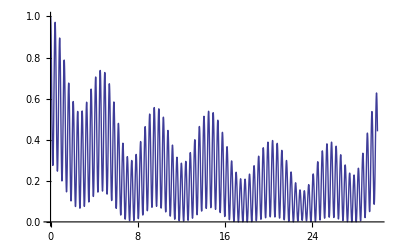

```mathematica
Plot[P[t,1],{t,0,30},AxesOrigin->{0,0}, PlotRange->{0,1}]
```

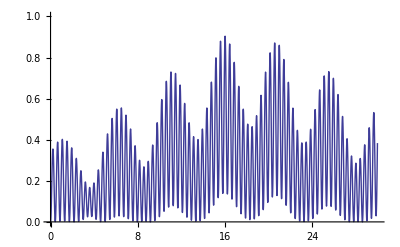

```mathematica
Plot[P[t,2],{t,0,30},AxesOrigin->{0,0}, PlotRange->{0,1}]
```

Those curves are oscillatory but (since the frequncy ratios are effectively irrational) aperiodic. The longest period

```mathematica
LongestOscillatoryPeriod=(2π)/AllProbFreqs⟦2⟧
```

118.967

far exceeds the t_max of the figures.

It was assumed above that the system is in a pure state. I omit discussion of the probability of finding the particle at the n^th node when the system is in an evolving mixed state.

### Continuous-time quantum walks

It is difficult—not on mathematical grounds, but on physical grounds—to imagine a quantum dynamical process that proceeds by discrete iterative jumps, so I concentrate here on continuous-time quantum walks.
Curiously, on the classical side of the street the situation is reversed: the random walk concept contains within its name an allusion to step-wise advance, and it is the notion of a "continuous walk" that calls for a leap of imagination (except for snakes and other slithery creatures?).

"Continuous-time quantum walk theory" is got by specializing the general theory reviewed in the preceding section. It is responsive to the question "How does one quantize the classical theory of continuous-time walks?" and unfolds in quite a straightforward manner, once one has established the context within which the theory functions, identified a natural point of departure. It is to that end that I interpolate here a

#### Review of the circumstances that permit a classical theory of continuous-time walks

NOTE: Here I borrow heavily from—and at certain points amplify—material in "Clasisical Master Equations" (26 October 2011).

Construct at random a non-symmetric Markov matrix (verifying that its columns are stochastic)

```mathematica
RowData=Table[Table[RandomReal[],{j,1,5}],{k,1,5}];
𝕄=Transpose[Table[RowData⟦k⟧/Total[RowData⟦k⟧],{k,1,5}]];
𝕄//MatrixForm
Table[Total[Transpose[𝕄]⟦k⟧],{k,1,5}]
```

(0.260171 | 0.253505 | 0.174834 | 0.332299 | 0.259082
0.0772768 | 0.259501 | 0.193551 | 0.0684383 | 0.290956
0.245622 | 0.150113 | 0.227104 | 0.335672 | 0.0607676
0.287002 | 0.204775 | 0.268498 | 0.104268 | 0.320391
0.129929 | 0.132107 | 0.136012 | 0.159322 | 0.0688026)

{1.,1.,1.,1.,1.}

and notice that its spectrum (which invariably has leading element = 1) typically includes complex numbers (and their conjugates), real numbers of both signs:

```mathematica
Eigenvalues[𝕄]
Abs[%]
```

{1.,-0.202902,0.0801992+0.0641059 ⅈ,0.0801992-0.0641059 ⅈ,-0.0376508}

{1.,0.202902,0.102672,0.102672,0.0376508}

Construct the (already normalized) right/left eigenvectors of 𝕄

```mathematica
Table[Subscript[e, k]=Eigenvectors[𝕄]⟦k⟧,{k,1,5}];
Table[Subscript[f, k]=Eigenvectors[Transpose[𝕄]]⟦k⟧,{k,1,5}];
```

and use those to assemble matrices

```mathematica
Table[Subscript[ℙ, n]=(Transpose[{Subscript[e, n]}].{Subscript[f, n]})/(Subscript[e, n].Subscript[f, n]),{n,1,5}];
```

These comprise a complete set of orthogonal projection matrices

```mathematica
Subscript[𝕆, 5]=({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
Subscript[𝕀, 5]=({{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 0, 0, 1}});
Chop[∑_(n=1)^5 Subscript[ℙ, n]]==Subscript[𝕀, 5]
Table[Chop[Subscript[ℙ, m].Subscript[ℙ, n]]==Subscript[𝕆, 5],{m,1,4},{n,m+1,5}]//TableForm
Table[Subscript[ℙ, n].Subscript[ℙ, n]==Subscript[ℙ, n],{n,1,5}]
```

True

True | True | True | True
True | True | True | 
True | True |  | 
True |  |  |

{True,True,True,True,True}

which are seen from

```mathematica
Table[Chop[Eigenvalues[Subscript[ℙ, n]]],{n,1,5}]
```

{{1.,0,0,0,0},{1.,0,0,0,0},{1.,0,0,0,0},{1.,0,0,0,0},{1.,0,0,0,0}}

to project onto 1-spaces. Giving names to the eigenvalues of 𝕄

```mathematica
Table[Subscript[λ, n]=Eigenvalues[𝕄]⟦n⟧,{n,1,5}];
```

we have this spectral representation of 𝕄:

```mathematica
Chop[𝕄-∑_(n=1)^5 Subscript[λ, n] Subscript[ℙ, n]]==Subscript[𝕆, 5]
```

True

Now construct

```mathematica
𝕃=∑_(k=1)^5 Log[Subscript[λ, k]] Subscript[ℙ, k];
```

(from which, by λ_1=1, the leading term is actually absent) and observe that 𝕃—the log of 𝕄—is typically complex:

```mathematica
𝕃//MatrixForm
```

(-1.92176+0.67744 ⅈ | 0.75383+0.390189 ⅈ | 0.353203+1.0493 ⅈ | 0.158738-1.22832 ⅈ | 1.98231-1.41645 ⅈ
-0.489878+0.280846 ⅈ | -1.49968+0.483353 ⅈ | 0.748163+0.645739 ⅈ | 0.278819+0.630318 ⅈ | 1.00232-3.36193 ⅈ
1.23056+0.144043 ⅈ | -0.124973-0.167524 ⅈ | -2.06744+0.0589702 ⅈ | 0.543717-1.14877 ⅈ | 0.300646+1.86006 ⅈ
0.698881-0.812242 ⅈ | 0.493471-0.273061 ⅈ | 0.436747-1.13046 ⅈ | -1.21397+2.1629 ⅈ | -0.561253+0.0178048 ⅈ
0.482203-0.290087 ⅈ | 0.377351-0.432958 ⅈ | 0.52933-0.623543 ⅈ | 0.232696-0.416128 ⅈ | -2.72402+2.90052 ⅈ)

Exponentiation of 𝕃 nevertheless gives back the real-valued matrix 𝕄

```mathematica
MatrixExp[𝕃]//Chop//MatrixForm
𝕄//MatrixForm
```

(0.260171 | 0.253505 | 0.174834 | 0.332299 | 0.259082
0.0772768 | 0.259501 | 0.193551 | 0.0684383 | 0.290956
0.245622 | 0.150113 | 0.227104 | 0.335672 | 0.0607676
0.287002 | 0.204775 | 0.268498 | 0.104268 | 0.320391
0.129929 | 0.132107 | 0.136012 | 0.159322 | 0.0688026)

(0.260171 | 0.253505 | 0.174834 | 0.332299 | 0.259082
0.0772768 | 0.259501 | 0.193551 | 0.0684383 | 0.290956
0.245622 | 0.150113 | 0.227104 | 0.335672 | 0.0607676
0.287002 | 0.204775 | 0.268498 | 0.104268 | 0.320391
0.129929 | 0.132107 | 0.136012 | 0.159322 | 0.0688026)

Similarly,

```mathematica
Chop[MatrixExp[2𝕃]-MatrixPower[𝕄,2]]==Subscript[𝕆, 5]
```

True

Mathematica knows how to raise matrices to non-integral powers, and indeed gives results identical to those produced by the method just devised: compare (for example)

```mathematica
MatrixExp[.5𝕃]//Chop//MatrixForm
MatrixPower[𝕄,.5]//Chop//MatrixForm
```

(0.390181+0.0650193 ⅈ | 0.191077+0.0208692 ⅈ | 0.0685572+0.0898446 ⅈ | 0.272803-0.176643 ⅈ | 0.366377+0.00710849 ⅈ
-0.0242303+0.00564444 ⅈ | 0.454131+0.0314849 ⅈ | 0.154545+0.0272438 ⅈ | 0.0158862+0.0898105 ⅈ | 0.415337-0.255405 ⅈ
0.240411+0.0304238 ⅈ | 0.0670072-0.0133474 ⅈ | 0.384313+0.0268948 ⅈ | 0.310868-0.164553 ⅈ | -0.053292+0.202743 ⅈ
0.268087-0.0908639 ⅈ | 0.163084-0.0111931 ⅈ | 0.244906-0.113781 ⅈ | 0.265822+0.310538 ⅈ | 0.16126-0.164993 ⅈ
0.12555-0.0102236 ⅈ | 0.1247-0.0278136 ⅈ | 0.147679-0.0302026 ⅈ | 0.134621-0.0591528 ⅈ | 0.110318+0.210547 ⅈ)

(0.390181+0.0650193 ⅈ | 0.191077+0.0208692 ⅈ | 0.0685572+0.0898446 ⅈ | 0.272803-0.176643 ⅈ | 0.366377+0.00710849 ⅈ
-0.0242303+0.00564444 ⅈ | 0.454131+0.0314849 ⅈ | 0.154545+0.0272438 ⅈ | 0.0158862+0.0898105 ⅈ | 0.415337-0.255405 ⅈ
0.240411+0.0304238 ⅈ | 0.0670072-0.0133474 ⅈ | 0.384313+0.0268948 ⅈ | 0.310868-0.164553 ⅈ | -0.053292+0.202743 ⅈ
0.268087-0.0908639 ⅈ | 0.163084-0.0111931 ⅈ | 0.244906-0.113781 ⅈ | 0.265822+0.310538 ⅈ | 0.16126-0.164993 ⅈ
0.12555-0.0102236 ⅈ | 0.1247-0.0278136 ⅈ | 0.147679-0.0302026 ⅈ | 0.134621-0.0591528 ⅈ | 0.110318+0.210547 ⅈ)

But those matrices are complex, so at non-integral times Markov's construction

(p_1
p_2
⋮
p_N)_t=Power[𝕄,t].(p_1
p_2
⋮
p_N)_0

leads to "stochastic vectors" which—since complex—are uninterpretable. Such 𝕄-matrices cannot be used to generate "continuous classical walks."

To enforce spectral reality we require might 𝕄 to be symmetric (we might, in other words, impose  "detailed balance"). We construct at random a symmetric Markov matrix

```mathematica
a=Table[RandomReal[],{k,1,5}];
b=Table[RandomReal[],{k,1,4}];
c=Table[RandomReal[],{k,1,3}];
d=Table[RandomReal[],{k,1,2}];
e=Table[RandomReal[],{k,1,1}];
Subscript[Row, 1]=a/Total[a];
Subscript[Row, 2]=Join[{Subscript[Row, 1]⟦2⟧},(1-Subscript[Row, 1]⟦2⟧)/Total[b] b];
Subscript[Row, 3]=Join[{Subscript[Row, 1]⟦3⟧,Subscript[Row, 2]⟦3⟧},(1-Subscript[Row, 1]⟦3⟧-Subscript[Row, 2]⟦3⟧)/Total[c] c];
Subscript[Row, 4]=Join[{Subscript[Row, 1]⟦4⟧,Subscript[Row, 2]⟦4⟧,Subscript[Row, 3]⟦4⟧},(1-Subscript[Row, 1]⟦4⟧-Subscript[Row, 2]⟦4⟧-Subscript[Row, 3]⟦4⟧)/Total[d] d];
Subscript[Row, 5]=Join[{Subscript[Row, 1]⟦5⟧,Subscript[Row, 2]⟦5⟧,Subscript[Row, 3]⟦5⟧,Subscript[Row, 4]⟦5⟧},(1-Subscript[Row, 1]⟦5⟧-Subscript[Row, 2]⟦5⟧-Subscript[Row, 3]⟦5⟧-Subscript[Row, 4]⟦5⟧)/Total[e] e];
Subscript[𝕄, sym]={Subscript[Row, 1],Subscript[Row, 2],Subscript[Row, 3],Subscript[Row, 4],Subscript[Row, 5]};

Subscript[𝕄, sym]//MatrixForm
Table[Total[Transpose[Subscript[𝕄, sym]]⟦k⟧],{k,1,5}]
```

(0.377226 | 0.420985 | 0.130224 | 0.0682567 | 0.00330842
0.420985 | 0.259297 | 0.206134 | 0.106328 | 0.00725638
0.130224 | 0.206134 | 0.162374 | 0.224525 | 0.276743
0.0682567 | 0.106328 | 0.224525 | 0.290028 | 0.310862
0.00330842 | 0.00725638 | 0.276743 | 0.310862 | 0.40183)

{1.,1.,1.,1.,1.}

with, as we verify, a real spectrum:

```mathematica
Eigenvalues[Subscript[𝕄, sym]]
```

{1.,0.640669,-0.148814,-0.0284719,0.027372}

but spectral reality does not enforce spectral positivity, and if any eigenvalues are in fact negative then

```mathematica
Log[Eigenvalues[Subscript[𝕄, sym]]]//Chop
```

{0,-0.445242,-1.90506+3.14159 ⅈ,-3.55884+3.14159 ⅈ,-3.59823}

and we are led back to the same problem as before, as I demonstrate:

```mathematica
Table[Subscript[es, k]=Eigenvectors[Subscript[𝕄, sym]]⟦k⟧,{k,1,5}];
Table[Subscript[fs, k]=Eigenvectors[Transpose[Subscript[𝕄, sym]]]⟦k⟧,{k,1,5}];
Table[Subscript[ℙs, n]=(Transpose[{Subscript[es, n]}].{Subscript[fs, n]})/(Subscript[es, n].Subscript[fs, n]),{n,1,5}];
Table[Subscript[λs, n]=Eigenvalues[Subscript[𝕄, sym]]⟦n⟧,{n,1,5}];
Chop[Subscript[𝕄, sym]-∑_(n=1)^5 Subscript[λs, n] Subscript[ℙs, n]]==Subscript[𝕆, 5]
Subscript[𝕃, sym]=∑_(k=1)^5 Log[Subscript[λs, k]] Subscript[ℙs, k];
Subscript[𝕃, sym]//MatrixForm
MatrixExp[Subscript[𝕃, sym]]//Chop//MatrixForm
Subscript[𝕄, sym]//MatrixForm
MatrixExp[.5 Subscript[𝕃, sym]]//Chop//MatrixForm
MatrixPower[Subscript[𝕄, sym],.5]//Chop//MatrixForm
```

True

(-1.48835+1.42276 ⅈ | 1.02325-1.45202 ⅈ | 0.829979-0.461552 ⅈ | 0.13729+0.288108 ⅈ | -0.502165+0.202706 ⅈ
1.02325-1.45202 ⅈ | -1.35981+1.84301 ⅈ | -0.0459997-0.418974 ⅈ | 0.184471-0.219472 ⅈ | 0.198093+0.247453 ⅈ
0.829979-0.461552 ⅈ | -0.0459997-0.418974 ⅈ | -2.40258+2.34322 ⅈ | 0.885663-0.277224 ⅈ | 0.732935-1.18547 ⅈ
0.13729+0.288108 ⅈ | 0.184471-0.219472 ⅈ | 0.885663-0.277224 ⅈ | -2.5176+0.0737364 ⅈ | 1.31017+0.134852 ⅈ
-0.502165+0.202706 ⅈ | 0.198093+0.247453 ⅈ | 0.732935-1.18547 ⅈ | 1.31017+0.134852 ⅈ | -1.73904+0.600459 ⅈ)

(0.377226 | 0.420985 | 0.130224 | 0.0682567 | 0.00330842
0.420985 | 0.259297 | 0.206134 | 0.106328 | 0.00725638
0.130224 | 0.206134 | 0.162374 | 0.224525 | 0.276743
0.0682567 | 0.106328 | 0.224525 | 0.290028 | 0.310862
0.00330842 | 0.00725638 | 0.276743 | 0.310862 | 0.40183)

(0.377226 | 0.420985 | 0.130224 | 0.0682567 | 0.00330842
0.420985 | 0.259297 | 0.206134 | 0.106328 | 0.00725638
0.130224 | 0.206134 | 0.162374 | 0.224525 | 0.276743
0.0682567 | 0.106328 | 0.224525 | 0.290028 | 0.310862
0.00330842 | 0.00725638 | 0.276743 | 0.310862 | 0.40183)

(0.468766+0.118804 ⅈ | 0.412205-0.145771 ⅈ | 0.142953+0.0218992 ⅈ | 0.0283299+0.0189943 ⅈ | -0.0522544-0.0139264 ⅈ
0.412205-0.145771 ⅈ | 0.370166+0.207382 ⅈ | 0.150419-0.097166 ⅈ | 0.0798836-0.0174168 ⅈ | -0.0126738+0.0529715 ⅈ
0.142953+0.0218992 ⅈ | 0.150419-0.097166 ⅈ | 0.219978+0.177284 ⅈ | 0.209694-0.0110126 ⅈ | 0.276956-0.0910046 ⅈ
0.0283299+0.0189943 ⅈ | 0.0798836-0.0174168 ⅈ | 0.209694-0.0110126 ⅈ | 0.400536+0.00425272 ⅈ | 0.281556+0.00518232 ⅈ
-0.0522544-0.0139264 ⅈ | -0.0126738+0.0529715 ⅈ | 0.276956-0.0910046 ⅈ | 0.281556+0.00518232 ⅈ | 0.506417+0.0467772 ⅈ)

(0.468766+0.118804 ⅈ | 0.412205-0.145771 ⅈ | 0.142953+0.0218992 ⅈ | 0.0283299+0.0189943 ⅈ | -0.0522544-0.0139264 ⅈ
0.412205-0.145771 ⅈ | 0.370166+0.207382 ⅈ | 0.150419-0.097166 ⅈ | 0.0798836-0.0174168 ⅈ | -0.0126738+0.0529715 ⅈ
0.142953+0.0218992 ⅈ | 0.150419-0.097166 ⅈ | 0.219978+0.177284 ⅈ | 0.209694-0.0110126 ⅈ | 0.276956-0.0910046 ⅈ
0.0283299+0.0189943 ⅈ | 0.0798836-0.0174168 ⅈ | 0.209694-0.0110126 ⅈ | 0.400536+0.00425272 ⅈ | 0.281556+0.00518232 ⅈ
-0.0522544-0.0139264 ⅈ | -0.0126738+0.0529715 ⅈ | 0.276956-0.0910046 ⅈ | 0.281556+0.00518232 ⅈ | 0.506417+0.0467772 ⅈ)

Symmetry, by itself, has not served to make meaningful the concept of a "continuous-time random walk." One telling fact has, however, emerged: While the columns of 𝕃 all sum to zero (as the columns of 𝕄 all sum to unity) , the rows of 𝕃 sum to a variety of non-zero values

```mathematica
Table[Total[Transpose[𝕃]⟦k⟧],{k,1,5}]//Chop
Table[Total[𝕃⟦k⟧],{k,1,5}]//Chop
```

{0,0,0,0,0}

{1.32631-0.527844 ⅈ,0.0397419-1.32168 ⅈ,-0.117496+0.746778 ⅈ,-0.146122-0.0350592 ⅈ,-1.10244+1.1378 ⅈ}

the log (or "generator") 𝕃_sym of 𝕄_sym is itself symmetric (but not, as one might anticipate, hermitian), so columns/rows both sum to zero

```mathematica
Table[Total[Transpose[Subscript[𝕃, sym]]⟦k⟧],{k,1,5}]//Chop
Table[Total[Subscript[𝕃, sym]⟦k⟧],{k,1,5}]//Chop
```

{0,0,0,0,0}

{0,0,0,0,0}

In that respect (though complex) it resembles the "Laplacian matrix" of a weighted graph.

We are motivated by this observation to construct at random a real-valued Laplacian matrix

```mathematica
𝕒={Join[{0},Table[RandomReal[],{k,1,4}]],
Join[{0,0},Table[RandomReal[],{k,1,3}]],
Join[{0,0,0},Table[RandomReal[],{k,1,2}]],
Join[{0,0,0,0},Table[RandomReal[],{k,1,1}]],
{0,0,0,0,0}};

𝕓=𝕒+Transpose[𝕒];

𝕕=DiagonalMatrix[Table[Total[𝕓⟦k⟧],{k,1,5}]];

𝕃ap=𝕓-𝕕;
𝕃ap//MatrixForm
```

(-2.5419 | 0.55347 | 0.966553 | 0.32905 | 0.692824
0.55347 | -2.43123 | 0.879725 | 0.138417 | 0.85962
0.966553 | 0.879725 | -2.93251 | 0.945772 | 0.140462
0.32905 | 0.138417 | 0.945772 | -2.01323 | 0.599988
0.692824 | 0.85962 | 0.140462 | 0.599988 | -2.29289)

We verify that this real symmetric matrix does possess the anticipated properties

```mathematica
Table[Total[𝕃ap⟦k⟧],{k,1,5}]//Chop
Eigenvalues[𝕃ap]//Chop
```

{0,0,0,0,0}

{-4.23877,-3.09386,-2.67429,-2.20484,0}

and use it to construct a real symmetric matrix (here the subscript is intended to suggest "continuous")

```mathematica
Subscript[𝕄, c]=MatrixExp[𝕃ap];
Subscript[𝕄, c]//MatrixForm
```

(0.237336 | 0.19301 | 0.201408 | 0.176499 | 0.191747
0.19301 | 0.246766 | 0.195469 | 0.162348 | 0.202406
0.201408 | 0.195469 | 0.228054 | 0.203665 | 0.171404
0.176499 | 0.162348 | 0.203665 | 0.274933 | 0.182555
0.191747 | 0.202406 | 0.171404 | 0.182555 | 0.251887)

that we demonstrate remains real in continuous time (i.e., when raised to all fractional powers)

```mathematica
Manipulate[MatrixForm[MatrixExp[t 𝕃ap]],{t, 0,2,0.1}]
```

and which at all times remains "Markovian" in the sense that its elements remain always positive and all columns sum at all times to unity:

```mathematica
Manipulate[Table[Total[MatrixExp[t 𝕃ap]]⟦k⟧,{k,1,5}],{t,0,2,0.1}]
```

OPEN QUESTION: Is it possible to devise a simple criterion that would enable one to discover "by inspection" whether or not the logarithm (or "generator") a given Markov matrix 𝕄 matrix is real?

#### Quantization of the preceding continuous-time classical walk

This is accomplished by in place of

𝕄[t_]:=MatrixExp[t 𝕃ap]

writing

```mathematica
𝕌[t_]:=MatrixExp[-ⅈ t 𝕃ap]
```

We have, in effect, assigned to the real symmetric (therefore hermitian) matrix 𝕃ap the role of a Hamiltonian, if one of specialized design—and it is solely in this respect that the quantum theory of random walks becomes a special instance of the general theory of quantum motion on discrete spaces.

The  ⅈ —the solitary detail that distinguishes the quantum theory from the classical theory—makes all the difference. And a major difference it is. We know, for example, that classically the system proceeds to an asymptotically equilibrated state:

```mathematica
Limit[Chop[MatrixExp[t 𝕃ap].({{1}, {0}, {0}, {0}, {0}})], t->∞]//MatrixForm
```

(0.2
0.2
0.2
0.2
0.2)

while in quantum theory the evolution of that (or any) state is oscillatory:

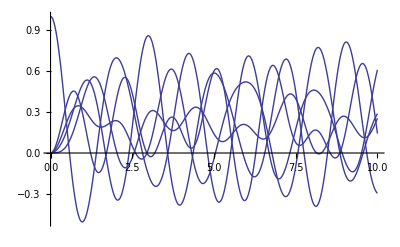

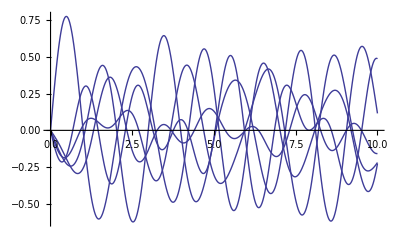

```mathematica
Plot[Re[𝕌[t].({{1}, {0}, {0}, {0}, {0}})],{t,0,10}]
Plot[Im[𝕌[t].({{1}, {0}, {0}, {0}, {0}})],{t,0,10}]
```

The unitary matrices that refer to quantum walks are distinguished from 𝕌-matrices-in-general in several ways. First, they are—compare

```mathematica
𝕌[t]⟦1⟧⟦2⟧//Chop
𝕌[t]⟦2⟧⟦1⟧//Chop
```

0.2+0.0804232 (Cos[2.20484 t]+ⅈ Sin[2.20484 t])+0.044286 (Cos[2.67429 t]+ⅈ Sin[2.67429 t])-0.460424 (Cos[3.09386 t]+ⅈ Sin[3.09386 t])+0.135715 (Cos[4.23877 t]+ⅈ Sin[4.23877 t])

0.2+0.0804232 (Cos[2.20484 t]+ⅈ Sin[2.20484 t])+0.044286 (Cos[2.67429 t]+ⅈ Sin[2.67429 t])-0.460424 (Cos[3.09386 t]+ⅈ Sin[3.09386 t])+0.135715 (Cos[4.23877 t]+ⅈ Sin[4.23877 t])

—symmetric, so can be inverted by simple conjugation. Demonstration of this point involves, however, such heavy calculation that I look only to one of the diagonal and one of the off-diagonal terms in the product:

```mathematica
Part[𝕌[Re[t]].Conjugate[𝕌[Re[t]]],1,1]/.Re[t]->t//FullSimplify//Chop
```

1.

```mathematica
Part[𝕌[Re[t]].Conjugate[𝕌[Re[t]]],1,2]/.Re[t]->t//FullSimplify//Chop//Chop
```

0

Moreover, such 𝕌-matrices inherit from their classical Markovian ancstors the property that the (complex) elements in each column/row sum to unity. Looking in this regard to the first column, we have

```mathematica
Table[Chop[𝕌[t]⟦j⟧⟦1⟧],{j,1,5}]//TrigToExp//MatrixForm
Total[%]//Chop
```

(0.2+0.0289574 ⅇ^(2.20484 ⅈ t)+0.137493 ⅇ^(2.67429 ⅈ t)+0.502326 ⅇ^(3.09386 ⅈ t)+0.131224 ⅇ^(4.23877 ⅈ t)
0.2+0.0804232 ⅇ^(2.20484 ⅈ t)+0.044286 ⅇ^(2.67429 ⅈ t)-0.460424 ⅇ^(3.09386 ⅈ t)+0.135715 ⅇ^(4.23877 ⅈ t)
0.2-0.028439 ⅇ^(2.20484 ⅈ t)+0.182944 ⅇ^(2.67429 ⅈ t)-0.0957011 ⅇ^(3.09386 ⅈ t)-0.258803 ⅇ^(4.23877 ⅈ t)
0.2-0.13419 ⅇ^(2.20484 ⅈ t)-0.0911259 ⅇ^(2.67429 ⅈ t)-0.0901439 ⅇ^(3.09386 ⅈ t)+0.115459 ⅇ^(4.23877 ⅈ t)
0.2+0.0532481 ⅇ^(2.20484 ⅈ t)-0.273596 ⅇ^(2.67429 ⅈ t)+0.143943 ⅇ^(3.09386 ⅈ t)-0.123595 ⅇ^(4.23877 ⅈ t))

1.

Looking now similarly to the full set of five columns, we have

```mathematica
Table[Chop[Total[Table[𝕌[t]⟦j⟧⟦k⟧,{j,1,5}]]],{k,1,5}]
```

{1.,1.,1.,1.,1.}

We are not surprised to discover that the complex exponentials shown above revolve with angular frequencies derived from the spectrum of the generator, 𝕃ap:

```mathematica
Table[Subscript[Ω, k]=-Eigenvalues[𝕃ap]⟦k⟧,{k,1,5}];
Reverse[Table[Subscript[Ω, k],{k,1,5}]]
```

{0.,2.20484,2.67429,3.09386,4.23877}

### Classical vs. quantum evolution of probability & entropy

The following figures tell the story:

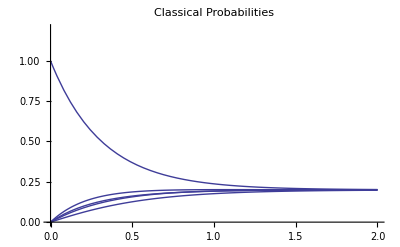

```mathematica
Plot[Table[Part[MatrixExp[t 𝕃ap].({{1}, {0}, {0}, {0}, {0}}),k],{k,1,5}],{t,0,2},PlotRange->{0,1.2}, PlotLabel->"Classical Probabilities"]
```

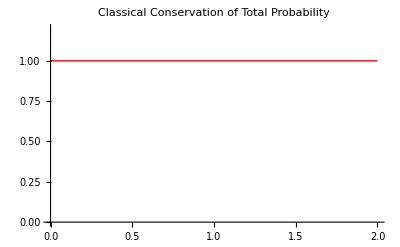

```mathematica
Plot[Total[Table[Part[MatrixExp[t 𝕃ap].({{1}, {0}, {0}, {0}, {0}}),k],{k,1,5}]],{t,0,2},PlotRange->{0,1.2}, PlotStyle->{Thick , Red}, PlotLabel->"Classical Conservation of Total Probability"]
```

```mathematica
ψ[t_,k_]:=Chop[Part[MatrixExp[ⅈ t 𝕃ap].({{1}, {0}, {0}, {0}, {0}}),k]]
```

```mathematica
QProb[t_,k_]:=Chop[TrigReduce[ψ[Re[t],k]Conjugate[ψ[Re[t],k]]/.Re[t]->t]]⟦1⟧
```

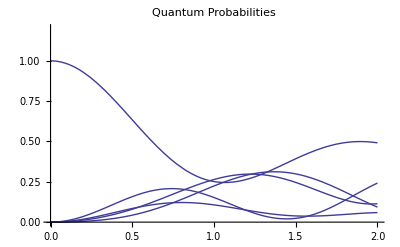

```mathematica
Plot[Table[QProb[t,k],{k,1,5}],{t,0,2},PlotRange->{0,1.2}, PlotLabel->"Quantum Probabilities"]
```

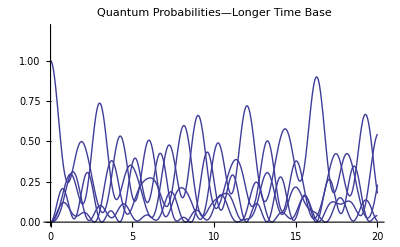

```mathematica
Plot[Table[QProb[t,k],{k,1,5}],{t,0,20},PlotRange->{0,1.2}, PlotLabel->"Quantum Probabilities—Longer Time Base"]
```

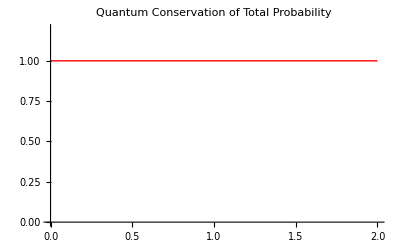

```mathematica
Plot[Total[Table[QProb[t,k],{k,1,5}]],{t,0,2},PlotRange->{0,1.2},  PlotStyle->{Thick , Red}, PlotLabel->"Quantum Conservation of Total Probability"]
```

The preceding "Quantum Probabilities" figure is a bit of a tangle; here I resolve it into its component parts:

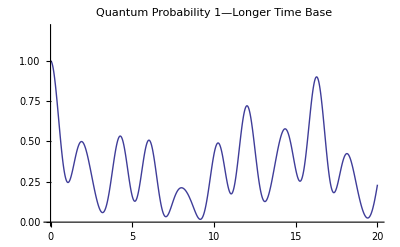

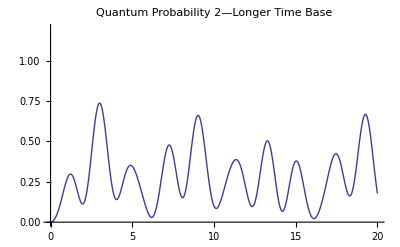

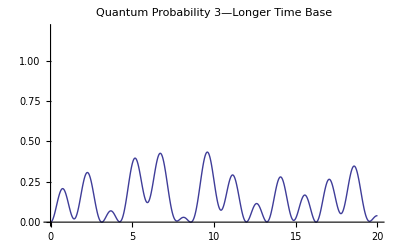

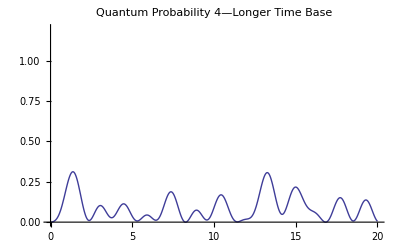

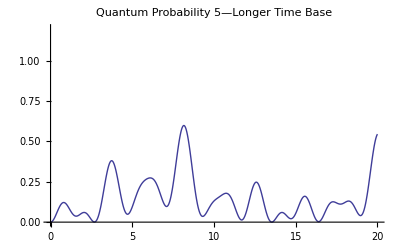

```mathematica
Plot[QProb[t,1],{t,0,20},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 1—Longer Time Base"]
Plot[QProb[t,2],{t,0,20},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 2—Longer Time Base"]
Plot[QProb[t,3],{t,0,20},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 3—Longer Time Base"]
Plot[QProb[t,4],{t,0,20},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 4—Longer Time Base"]
Plot[QProb[t,5],{t,0,20},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 5—Longer Time Base"]
```

[The following remark was motivated by a the curves that resulted from a different random 𝕃ap; I retain them, even though they are this time around less apt.] It is interesting that QP1 remains relatively larger than the others, interesting also that QP3 is so nearly periodic. Do those features persist in the longer term? On the following evidence, they seem to :

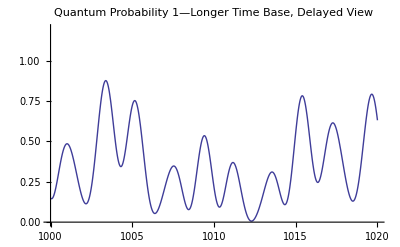

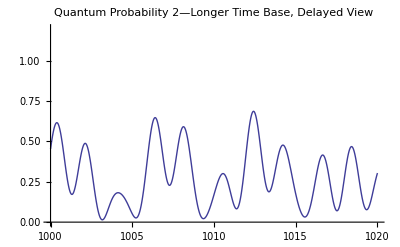

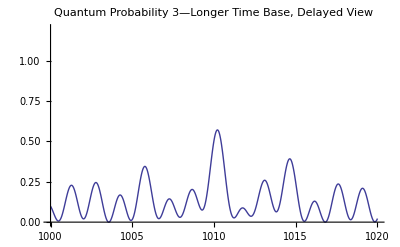

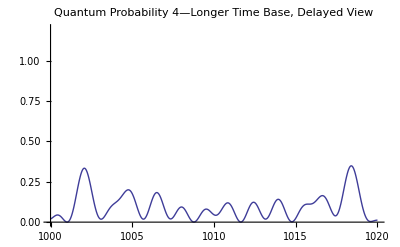

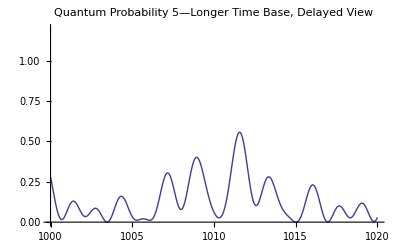

```mathematica
Plot[QProb[t,1],{t,1000,1020},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 1—Longer Time Base, Delayed View"]
Plot[QProb[t,2],{t,1000,1020},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 2—Longer Time Base, Delayed View"]
Plot[QProb[t,3],{t,1000,1020},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 3—Longer Time Base, Delayed View"]
Plot[QProb[t,4],{t,1000,1020},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 4—Longer Time Base, Delayed View"]
Plot[QProb[t,5],{t,1000,1020},PlotRange->{0,1.2}, PlotLabel->"Quantum Probability 5—Longer Time Base, Delayed View"]
```

I look finally to the ENTROPIES of the evolving classical/quantum distributions:

```mathematica
Ent[x_]:=-x Log[x]
```

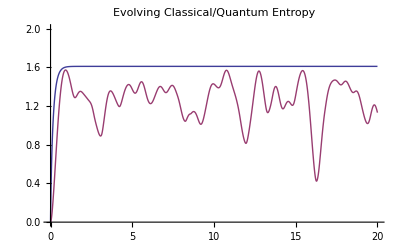

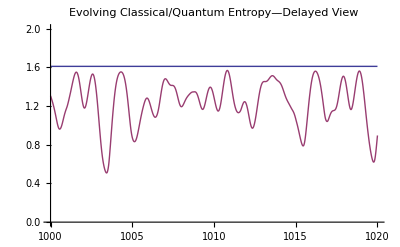

```mathematica
Plot[{Sum[Ent[Part[MatrixExp[t 𝕃ap].({{1}, {0}, {0}, {0}, {0}}),k]],{k,1,5}],Sum[Ent[QProb[t,k]],{k,1,5}]},{t,0,20},PlotRange->{0,2}, PlotLabel->"Evolving Classical/Quantum Entropy"]
Plot[{Sum[Ent[Part[MatrixExp[t 𝕃ap].({{1}, {0}, {0}, {0}, {0}}),k]],{k,1,5}],Sum[Ent[QProb[t,k]],{k,1,5}]},{t,1000,1020},PlotRange->{0,2}, PlotLabel->"Evolving Classical/Quantum Entropy—Delayed View"]
```

It is not surprising that the classical entropy rises monotonically until it assumes the value of the asymptotically equilibrated state. More surprising is the evidence that the classical entropy always exceeds the quantum entropy, and that temporal variation of the latter is ocassionally so broad.

I will return later to consideration of this BASIC QUESTION: Does the preceding "quantum entropy" notation make physical sense? And—if so—why does it appear on its face to violate the spirit of the H-theorem?

Here as in the general theory, the angular frequencies that appear in the functions that contribute to those curves—see for example

```mathematica
QProb[t,1]
QProb[t,2]
```

0.329294+0.138132 Cos[0.419568 t]+0.00796287 Cos[0.469458 t]+0.0290921 Cos[0.889025 t]+0.131835 Cos[1.14491 t]+0.0360847 Cos[1.56448 t]+0.00759982 Cos[2.03394 t]+0.011583 Cos[2.20484 t]+0.0549971 Cos[2.67429 t]+0.20093 Cos[3.09386 t]+0.0524897 Cos[4.23877 t]

0.278838-0.0407807 Cos[0.419568 t]+0.00712324 Cos[0.469458 t]-0.0740575 Cos[0.889025 t]-0.124973 Cos[1.14491 t]+0.0120205 Cos[1.56448 t]+0.0218292 Cos[2.03394 t]+0.0321693 Cos[2.20484 t]+0.0177144 Cos[2.67429 t]-0.18417 Cos[3.09386 t]+0.054286 Cos[4.23877 t]

—are precisely the frequencies that appear in the following list:

```mathematica
Table[Subscript[Ω, k]=-Eigenvalues[𝕃ap]⟦k⟧,{k,1,5}];
DIFFS=Flatten[Table[Subscript[Ω, k]-Subscript[Ω, j],{k,1,5},{j,k,5}]];
SpectralDifferences=DeleteDuplicates[Sort[DIFFS]]
Length[%]
```

{0.,0.419568,0.469458,0.889025,1.14491,1.56448,2.03394,2.20484,2.67429,3.09386,4.23877}

11

### REMARK: "Wavepackets" in the quantum mechanics of discrete systems

When studying the quantum dynamics of a particle that moves in a continuum (x-space, p-space, phase space) we constructed interestingly-weighted superpositions of energy eigenstates

ψ_0[x]=∑_n c_n ψ_n[x]

and—after setting the eigenstates a-buzz—contemplate the motion either of

ψ[x,t]=∑_n c_n ⅇ^(-ⅈ ω_n t)ψ_n[x]

or (more conveniently) literally watch the graphable motion of

P[x,t]=Abs[ψ[x,t]]^2

But when the particle moves on a graph we have no such continuous variable as x to play with; we must make do with

ψ_0=∑_n c_n ψ_n    whence    ψ[t]=∑_n c_n ⅇ^(-ⅈ ω_n t)ψ_n

where the  ψ_n  are vector-valued. It is in that clumsy sense that

```mathematica
Plot[Table[QProb[t,k],{k,1,5}],{t,0,2},PlotRange->{0,1.2}, PlotLabel->"Quantum Probabilities"]
```

-Graphics-

describes the motion of a "wavepacket on a discrete space."  

If the particle moved on a lattice inscribed on the unbounded plane (or, more simply, on the unbonded line) we might expect to do better—might expect even to recover the results of continuum quantum mechanics in the "continuum limit."

### OPEN QUESTION: Does the theory of quantum walks possess a classical limit?

"Classical" equations of motion can be extracted from quantum dynamics in many ways: formally set ℏ→0, or look to the "limit of large quantum numbers," or look to the motion of quantum mechanical expectation values (Ehrenfest's theorem). But none of those devices are available to the quantum theory of walks on graphs (or, more generally, to any form of finite-dimensional quantum mechanics, which includes the quantum theory of angular momentum (spin), the pure/applied theory of qubits). Formally, the question is very simple: "How to get rid of the ⅈ?" But on what compelling physical grounds can one motivate the adjustment

MatrixExp[-ⅈ t 𝕃ap]⟹MatrixExp[t 𝕃ap]

SEE IN THIS CONNECTION THE  AFTERWORD  AT THE END OF THIS NOTEBOOK

### The reversibility-irreversibility distinction

Quantum dynamical processes mediated by

𝕌[t]=MatrixExp[-ⅈ t 𝕃ap]

make—in the absence of measurements—unobjectionable good sense when inverted. But

𝕄[t]=MatrixExp[ t 𝕃ap]

becomes non-Markovian when inverted. This is a profoundly consequential distinction, and serves to further complicate the problem of constructing a plausible classical limit of the quantum theory of walks on graphs.

### The especially simple quantum walks contemplated in the quantum walk literature

```mathematica
Needs["GraphUtilities`"];
```

Matt Jemalita, and the authors upon whose work he drew—see

```mathematica
Hyperlink["Andrew Childs et al","http://arxiv.org/abs/quant-ph/0209131"]
```

—restricted their attention to walks with generators that are "proportional to the adjacency matrix," or so they claim. Actually, their generators are (as mine also will be) proportional to the "normalized negatives" of unweighted Laplacian matrices:

```mathematica
Hyperlink["Laplacian of a Graph","http://en.wikipedia.org/wiki/Laplacian_matrix"]
```

Here—borrowing a routine from "Classical Master Equations" (26 October 2011) —I construct at random (with different results at each repetition) the adjacency matrix and associated Laplacian matrix of an 8-node graph:

(0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

(3 | 0 | 0 | 0 | -1 | -1 | 0 | -1
0 | 5 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 4 | -1 | -1 | 0 | -1 | -1
0 | -1 | -1 | 5 | -1 | 0 | -1 | -1
-1 | -1 | -1 | -1 | 5 | -1 | 0 | 0
-1 | -1 | 0 | 0 | -1 | 4 | -1 | 0
0 | -1 | -1 | -1 | 0 | -1 | 4 | 0
-1 | -1 | -1 | -1 | 0 | 0 | 0 | 4)

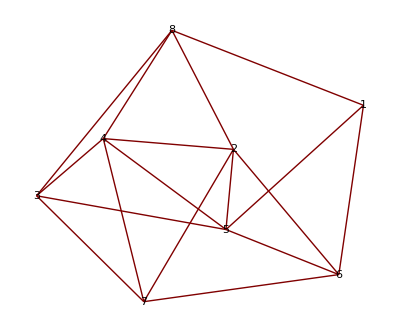

```mathematica
𝕒={Join[{0},Table[RandomInteger[],{k,1,7}]],
Join[{0,0},Table[RandomInteger[],{k,1,6}]],
Join[{0,0,0},Table[RandomInteger[],{k,1,5}]],
Join[{0,0,0,0},Table[RandomInteger[],{k,1,4}]],
Join[{0,0,0,0,0},Table[RandomInteger[],{k,1,3}]],
Join[{0,0,0,0,0,0},Table[RandomInteger[],{k,1,2}]],
Join[{0,0,0,0,0,0,0},Table[RandomInteger[],{k,1,1}]],
{0,0,0,0,0,0,0,0}};

𝔸=𝕒+Transpose[𝕒];
𝔸//MatrixForm
𝔻=DiagonalMatrix[Table[Total[𝔸⟦k⟧],{k,1,8}]];
𝕃=𝔻-𝔸;
𝕃//MatrixForm
GraphPlot[𝔸,VertexLabeling->True]
```

The spectrum of 𝕃

```mathematica
Table[Subscript[λ, k]=N[Eigenvalues[𝕃]]⟦k⟧,{k,1,8}];
Table[Subscript[λ, k],{k,1,8}]
```

{7.2239,6.45192,5.44392,4.73151,4.41274,3.21539,2.52062,0.}

is invariably positive-semidefinite, and invariably includes 0 at least once (more times if the graph is assembnled from disconnected fragments). From 𝕃 and its greatest eigenvalue we construct

```mathematica
𝕂=-𝕃/Subscript[λ, 1];
𝕂//MatrixForm
```

(-0.415288 | 0 | 0 | 0 | 0.138429 | 0.138429 | 0 | 0.138429
0 | -0.692147 | 0 | 0.138429 | 0.138429 | 0.138429 | 0.138429 | 0.138429
0 | 0 | -0.553717 | 0.138429 | 0.138429 | 0 | 0.138429 | 0.138429
0 | 0.138429 | 0.138429 | -0.692147 | 0.138429 | 0 | 0.138429 | 0.138429
0.138429 | 0.138429 | 0.138429 | 0.138429 | -0.692147 | 0.138429 | 0 | 0
0.138429 | 0.138429 | 0 | 0 | 0.138429 | -0.553717 | 0.138429 | 0
0 | 0.138429 | 0.138429 | 0.138429 | 0 | 0.138429 | -0.553717 | 0
0.138429 | 0.138429 | 0.138429 | 0.138429 | 0 | 0 | 0 | -0.553717)

which is found to possess a negative-semidefinite spectrum that invariably includes both -1 and 0 as members. Our interest in 𝕂 derives from the fact that it generates a symmetric Markovian matrix:

```mathematica
𝕄=MatrixExp[𝕂];
𝕄//MatrixForm
Table[Total[𝕄⟦k⟧],{k,1,8}]
```

(0.678826 | 0.0179431 | 0.0126481 | 0.0128783 | 0.0883469 | 0.0931968 | 0.00804468 | 0.0881162
0.0179431 | 0.528097 | 0.0230077 | 0.0879168 | 0.0835051 | 0.0879011 | 0.088339 | 0.0832905
0.0126481 | 0.0230077 | 0.598285 | 0.0929659 | 0.0832826 | 0.0131169 | 0.088355 | 0.0883386
0.0128783 | 0.0879168 | 0.0929659 | 0.528542 | 0.08329 | 0.0179359 | 0.0883546 | 0.0881164
0.0883469 | 0.0835051 | 0.0832826 | 0.08329 | 0.527889 | 0.0881241 | 0.022777 | 0.0227849
0.0931968 | 0.0879011 | 0.0131169 | 0.0179359 | 0.0881241 | 0.598492 | 0.0878855 | 0.0133478
0.00804468 | 0.088339 | 0.088355 | 0.0883546 | 0.022777 | 0.0878855 | 0.598285 | 0.0179592
0.0881162 | 0.0832905 | 0.0883386 | 0.0881164 | 0.0227849 | 0.0133478 | 0.0179592 | 0.598046)

{1.,1.,1.,1.,1.,1.,1.,1.}

REMARK: Had we omitted the minus sign from the definition of 𝕂 we would have been led by exponentiation to the inverse of 𝕄, which is non-Markovian.

#### Continuous-time quantum walk on an unweighted 3-cube

We look to the case

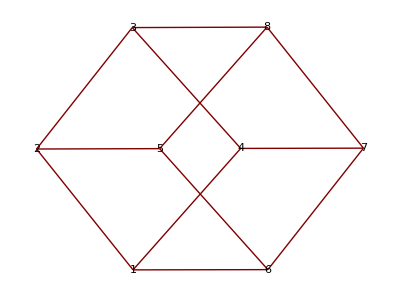

```mathematica
𝔸=({{0, 1, 0, 1, 0, 1, 0, 0}, {1, 0, 1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1, 0, 1}, {0, 0, 1, 0, 1, 0, 1, 0}});
GraphPlot[𝔸,VertexLabeling->True]
```

in which it will be noticed (though this is a matter of little consequence) that I have labeled vertices in such a way that the lables of diametric vertices add up in all cases to 9. The associated Laplacian matrix is

```mathematica
𝕃=3 IdentityMatrix[8]-𝔸;
𝕃//MatrixForm
```

(3 | -1 | 0 | -1 | 0 | -1 | 0 | 0
-1 | 3 | -1 | 0 | -1 | 0 | 0 | 0
0 | -1 | 3 | -1 | 0 | 0 | 0 | -1
-1 | 0 | -1 | 3 | 0 | 0 | -1 | 0
0 | -1 | 0 | 0 | 3 | -1 | 0 | -1
-1 | 0 | 0 | 0 | -1 | 3 | -1 | 0
0 | 0 | 0 | -1 | 0 | -1 | 3 | -1
0 | 0 | -1 | 0 | -1 | 0 | -1 | 3)

```mathematica
Eigenvalues[𝕃]
```

{6,4,4,4,2,2,2,0}

so the "normalized negative" of 𝕃 is

```mathematica
𝕂=-𝕃/6;
𝕂//MatrixForm
Eigenvalues[𝕂]
```

(-1/2 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 0
1/6 | -1/2 | 1/6 | 0 | 1/6 | 0 | 0 | 0
0 | 1/6 | -1/2 | 1/6 | 0 | 0 | 0 | 1/6
1/6 | 0 | 1/6 | -1/2 | 0 | 0 | 1/6 | 0
0 | 1/6 | 0 | 0 | -1/2 | 1/6 | 0 | 1/6
1/6 | 0 | 0 | 0 | 1/6 | -1/2 | 1/6 | 0
0 | 0 | 0 | 1/6 | 0 | 1/6 | -1/2 | 1/6
0 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | -1/2)

{-1,-2/3,-2/3,-2/3,-1/3,-1/3,-1/3,0}

Exponentiation yields a matrix 𝕄 which we show to be Markovian

```mathematica
𝕄=N[MatrixExp[𝕂]];
𝕄//MatrixForm
Table[Total[𝕄⟦k⟧],{k,1,8}]
Eigenvalues[𝕄]
```

(0.632216 | 0.104404 | 0.0172414 | 0.104404 | 0.0172414 | 0.104404 | 0.0172414 | 0.00284725
0.104404 | 0.632216 | 0.104404 | 0.0172414 | 0.104404 | 0.0172414 | 0.00284725 | 0.0172414
0.0172414 | 0.104404 | 0.632216 | 0.104404 | 0.0172414 | 0.00284725 | 0.0172414 | 0.104404
0.104404 | 0.0172414 | 0.104404 | 0.632216 | 0.00284725 | 0.0172414 | 0.104404 | 0.0172414
0.0172414 | 0.104404 | 0.0172414 | 0.00284725 | 0.632216 | 0.104404 | 0.0172414 | 0.104404
0.104404 | 0.0172414 | 0.00284725 | 0.0172414 | 0.104404 | 0.632216 | 0.104404 | 0.0172414
0.0172414 | 0.00284725 | 0.0172414 | 0.104404 | 0.0172414 | 0.104404 | 0.632216 | 0.104404
0.00284725 | 0.0172414 | 0.104404 | 0.0172414 | 0.104404 | 0.0172414 | 0.104404 | 0.632216)

{1.,1.,1.,1.,1.,1.,1.,1.}

{1.,0.716531,0.716531,0.716531,0.513417,0.513417,0.513417,0.367879}

but which has elements and eigenvalues that don't—on their face—seem to have much to do with cubes. But when raised to high powers (as one would do if looking to the asymptotics of classic walks on the cube) it assumes a form

```mathematica
MatrixPower[𝕄,50]//MatrixForm
```

(0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125)

that finally does speak of cubic symmetry, since

```mathematica
N[1/8]==0.125
```

True

And if we construct a random stochastic vector

```mathematica
q=Table[RandomReal[],{k,1,8}];
p=Transpose[{q/Total[q]}];
p//MatrixForm
```

(0.0757578
0.146794
0.0939359
0.105909
0.118904
0.194833
0.131614
0.132253)

we find that it goes asymptotically to an equilibrated state

```mathematica
MatrixPower[𝕄,50].p//MatrixForm
```

(0.125
0.125
0.125
0.125
0.125
0.125
0.125
0.125)

with

probability=1/8

at each of the 8 cubic vertices.


But look to the quantum mechanics: the unitary propagator is

```mathematica
𝕌[t_]:=MatrixExp[-ⅈ 𝕂 t]
```

This matrix is large (8 × 8) but its elements are remarkably simple: here is a typical diagonal element

```mathematica
𝕌[t]⟦1⟧⟦1⟧
```

1/8 (1+3 Cos[t/3]+3 Cos[(2 t)/3]+Cos[t]+ⅈ (3 Sin[t/3]+3 Sin[(2 t)/3]+Sin[t]))

and here (note the symmetry) are a pair of off-diiagonal elements.

```mathematica
𝕌[t]⟦1⟧⟦2⟧
𝕌[t]⟦2⟧⟦1⟧
```

1/8 (1+Cos[t/3]-Cos[(2 t)/3]-Cos[t]+ⅈ (Sin[t/3]-Sin[(2 t)/3]-Sin[t]))

1/8 (1+Cos[t/3]-Cos[(2 t)/3]-Cos[t]+ⅈ (Sin[t/3]-Sin[(2 t)/3]-Sin[t]))

Cubic symmetry has endowed the spectrum of 𝕂 with a high degree of degeneracy

```mathematica
Eigenvalues[𝕂]
```

{-1,-2/3,-2/3,-2/3,-1/3,-1/3,-1/3,0}

There are only four distinct spectral values

```mathematica
DeleteDuplicates[-Eigenvalues[𝕂]]
```

{1,2/3,1/3,0}

and those are precisely the angular frequencies seen in preceeding matrix elements, and also in the following list of evolving probability amplitudes:

```mathematica
ψ[t_]:=𝕌[t].({{1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
ψ[t]//MatrixForm
```

(1/8 (1+3 Cos[t/3]+3 Cos[(2 t)/3]+Cos[t]+ⅈ (3 Sin[t/3]+3 Sin[(2 t)/3]+Sin[t]))
1/8 (1+Cos[t/3]-Cos[(2 t)/3]-Cos[t]+ⅈ (Sin[t/3]-Sin[(2 t)/3]-Sin[t]))
1/8 (1-Cos[t/3]-Cos[(2 t)/3]+Cos[t]+ⅈ (-Sin[t/3]-Sin[(2 t)/3]+Sin[t]))
1/8 (1+Cos[t/3]-Cos[(2 t)/3]-Cos[t]+ⅈ (Sin[t/3]-Sin[(2 t)/3]-Sin[t]))
1/8 (1-Cos[t/3]-Cos[(2 t)/3]+Cos[t]+ⅈ (-Sin[t/3]-Sin[(2 t)/3]+Sin[t]))
1/8 (1+Cos[t/3]-Cos[(2 t)/3]-Cos[t]+ⅈ (Sin[t/3]-Sin[(2 t)/3]-Sin[t]))
1/8 (1-Cos[t/3]-Cos[(2 t)/3]+Cos[t]+ⅈ (-Sin[t/3]-Sin[(2 t)/3]+Sin[t]))
1/8 (1-3 Cos[t/3]+3 Cos[(2 t)/3]-Cos[t]+ⅈ (-3 Sin[t/3]+3 Sin[(2 t)/3]-Sin[t])))

Curiously—but obviously—those same values appear when one lists all possible spectral differences that can be assembled from those spectral values

```mathematica
Table[Subscript[ω, k]=DeleteDuplicates[-Eigenvalues[𝕂]]⟦k⟧,{k,1,4}];
SpectralDifferences=DeleteDuplicates[Sort[Flatten[Table[Subscript[ω, k]-Subscript[ω, j],{k,1,4},{j,k,4}]]]]
```

{0,1/3,2/3,1}

so we encounter no new frequencies when we to the associated list of evolving probabilities:

```mathematica
Ψ[t_,k_]:=Chop[Part[𝕌[t].({{1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}}),k]]
QProb[t_,k_]:=Chop[TrigReduce[Ψ[Re[t],k]Conjugate[Ψ[Re[t],k]]/.Re[t]->t]]⟦1⟧

EvolvingProbabilities=Table[QProb[t,k],{k,1,8}]
```

{1/32 (10+15 Cos[t/3]+6 Cos[(2 t)/3]+Cos[t]),1/32 (2+Cos[t/3]-2 Cos[(2 t)/3]-Cos[t]),1/32 (2-Cos[t/3]-2 Cos[(2 t)/3]+Cos[t]),1/32 (2+Cos[t/3]-2 Cos[(2 t)/3]-Cos[t]),1/32 (2-Cos[t/3]-2 Cos[(2 t)/3]+Cos[t]),1/32 (2+Cos[t/3]-2 Cos[(2 t)/3]-Cos[t]),1/32 (2-Cos[t/3]-2 Cos[(2 t)/3]+Cos[t]),1/32 (10-15 Cos[t/3]+6 Cos[(2 t)/3]-Cos[t])}

The motion is clearly periodic (eigenfrequency ratios are rational), with periods given by

```mathematica
Periods=(2π)/{1,2/3,1/3}//N
```

{6.28319,9.42478,18.8496}

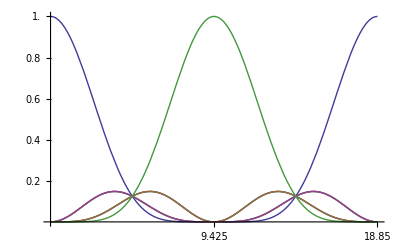

```mathematica
Plot[EvolvingProbabilities,{t,0,18.8496},PlotRange->{0,1},Ticks->{{9.425,18.85},{0.2, 0.4, 0.6, 0.8, 1.0}}]
```

The figure indicates that if the walker is known to be at vertex #1 at t = 0 then it will with certainty be found at the diametrically opposite vertex #8 at time t = 9.425, and that it sloshesback and forth with perfect periodicity. The simplicity of the situation owes everything to the symmetry of the cube. 


Looking to the evolving entropy of the probability distribution, we have

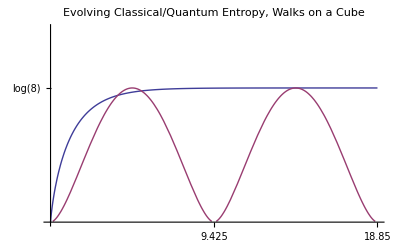

```mathematica
Plot[{Sum[Ent[Part[MatrixExp[t 𝕂].({{1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}}),k]],{k,1,8}],Sum[Ent[QProb[t,k]],{k,1,8}]},{t,0,18.8496},PlotRange->{0,3},
PlotRange->{0,3},Ticks->{{9.425,18.85},{Log[8]}},
GridLines->{{},{Log[8]}}, PlotLabel->"Evolving Classical/Quantum Entropy, Walks on a Cube"]
```

The entropy drops to zero whenever the state of the system is known with certainty…which is a circumstance that typically never recurs, but in this instance happens twice per period.

AFTERWORD

Earlier on, I was led to pose this

### OPEN QUESTION: Does the theory of quantum walks possess a classical limit?

After bringing this notebook to its present state of completion, I chanced (an hour ago) to be reading

```mathematica
Hyperlink["Decoherence in quantum walks—a review","http://arxiv.org/abs/quant-ph/0606016"]
```

by one Viv Kendon (2006), of the School of Physics & Astronomy, University of Leeds. Near the beginning of his §5 (page 19) Kendon remarks that "One way to justify a particular quantum dynamics as being a "quantum walk" is to see if it turns into a classical random walk when decohered. … Many early studies of quantum walks took the trouble to show numerically that, for specific cases, their quantum walks decohered into classical random walks… A more systematic treatment of the quantum to classical transition in a general quantum walk appears in

```mathematica
Hyperlink["Complementarity and quantum walks","http://arxiv.org/abs/quant-ph/0404043"]
```

where the authors (Kendon & B. C. Sanders, 2005) emphasize the importance of demonstrating that quantum walks exhibit both wave (pure quantum) and particle (decohered) dynamics and, for a non-unitary quantum walk, being able to interpolate between these two modes of behavior by turning the decoherence up or down."

That reference to non-unitary quantum motion—means precisely what?—puts me in mind of the quantum mechanics of open systems (Kossakowski-Lindblad equation)

```mathematica
Hyperlink["Lindblad equation","http://en.wikipedia.org/wiki/Lindblad_equation"]
```

[Google supplies many other helpful links] …which, after all, was my original destination when I took up this review of elementary quantum walk theory.

So that is the subject to which I now—finally—(re)turn.

ANOTHER AFTERWORD

### Distinction between discrete & continuous classical walks on a cube

Continous walks, if sampled at regular intervals, become discrete walks. I had on this ground always assumed that the continuous theory was primary, and gave back the discrete theory as a trivial special case…and therefore wondered how Frederick Strauch (recently an applicant for a position on the Reed College physics faculty) found anything to write about in

```mathematica
Hyperlink["Connecting the discrete- and continuous-time quantum walks","http://arxiv.org/pdf/quant-ph/0606050v1"]
```

But then I recalled that, in recent discussion of the discrete-time classical walk on the cube I used the transition matrix

```mathematica
𝕋=({{0, 1/3, 0, 1/3, 0, 1/3, 0, 0}, {1/3, 0, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 0, 1/3, 0, 0, 0, 1/3}, {1/3, 0, 1/3, 0, 0, 0, 1/3, 0}, {0, 1/3, 0, 0, 0, 1/3, 0, 1/3}, {1/3, 0, 0, 0, 1/3, 0, 1/3, 0}, {0, 0, 0, 1/3, 0, 1/3, 0, 1/3}, {0, 0, 1/3, 0, 1/3, 0, 1/3, 0}});
```

and encountered the "asymptotic blinking" phenomenon

```mathematica
MatrixPower[𝕋,20]//N//MatrixForm
MatrixPower[𝕋,21]//N//MatrixForm
```

(0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0.
0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25
0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0.
0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25
0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0.
0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25
0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0.
0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25)

(0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25
0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0.
0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25
0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0.
0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25
0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0.
0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25
0.25 | 0. | 0.25 | 0. | 0.25 | 0. | 0.25 | 0.)

𝕋 is a symmetric Markov matrix, but in the continuous-time theory I was led (at time t = 1) to a different symmetric Markov matrix

```mathematica
𝕄//MatrixForm
```

(0.632216 | 0.104404 | 0.0172414 | 0.104404 | 0.0172414 | 0.104404 | 0.0172414 | 0.00284725
0.104404 | 0.632216 | 0.104404 | 0.0172414 | 0.104404 | 0.0172414 | 0.00284725 | 0.0172414
0.0172414 | 0.104404 | 0.632216 | 0.104404 | 0.0172414 | 0.00284725 | 0.0172414 | 0.104404
0.104404 | 0.0172414 | 0.104404 | 0.632216 | 0.00284725 | 0.0172414 | 0.104404 | 0.0172414
0.0172414 | 0.104404 | 0.0172414 | 0.00284725 | 0.632216 | 0.104404 | 0.0172414 | 0.104404
0.104404 | 0.0172414 | 0.00284725 | 0.0172414 | 0.104404 | 0.632216 | 0.104404 | 0.0172414
0.0172414 | 0.00284725 | 0.0172414 | 0.104404 | 0.0172414 | 0.104404 | 0.632216 | 0.104404
0.00284725 | 0.0172414 | 0.104404 | 0.0172414 | 0.104404 | 0.0172414 | 0.104404 | 0.632216)

which at asymptotic times does not exhibit blinking

```mathematica
MatrixPower[𝕄,50]//MatrixForm
```

(0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125)

and in fact becomes the average of the two 𝕋-asymptotes.

𝕋  refers to a process in which lingering is disallowed, and the next step takes the walker—with equal probabilities—to one or another of the three adjacent vertices.  Continuous walks, on the other hand, are generated by a matrix

```mathematica
𝕂//MatrixForm
```

(-1/2 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 0
1/6 | -1/2 | 1/6 | 0 | 1/6 | 0 | 0 | 0
0 | 1/6 | -1/2 | 1/6 | 0 | 0 | 0 | 1/6
1/6 | 0 | 1/6 | -1/2 | 0 | 0 | 1/6 | 0
0 | 1/6 | 0 | 0 | -1/2 | 1/6 | 0 | 1/6
1/6 | 0 | 0 | 0 | 1/6 | -1/2 | 1/6 | 0
0 | 0 | 0 | 1/6 | 0 | 1/6 | -1/2 | 1/6
0 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | -1/2)

which differs from but is an obviously close relative of 𝕋:

```mathematica
Subscript[𝕀, 8]=IdentityMatrix[8];
```

```mathematica
𝕂==-1/2 Subscript[𝕀, 8]+1/2 𝕋
```

True

At short times

```mathematica
𝕄[t]=MatrixExp[t 𝕂]
```

becomes

```mathematica
Subscript[𝕄, τ]=Subscript[𝕀, 8]+τ 𝕂;
Subscript[𝕄, τ]//MatrixForm
```

(1-τ/2 | τ/6 | 0 | τ/6 | 0 | τ/6 | 0 | 0
τ/6 | 1-τ/2 | τ/6 | 0 | τ/6 | 0 | 0 | 0
0 | τ/6 | 1-τ/2 | τ/6 | 0 | 0 | 0 | τ/6
τ/6 | 0 | τ/6 | 1-τ/2 | 0 | 0 | τ/6 | 0
0 | τ/6 | 0 | 0 | 1-τ/2 | τ/6 | 0 | τ/6
τ/6 | 0 | 0 | 0 | τ/6 | 1-τ/2 | τ/6 | 0
0 | 0 | 0 | τ/6 | 0 | τ/6 | 1-τ/2 | τ/6
0 | 0 | τ/6 | 0 | τ/6 | 0 | τ/6 | 1-τ/2)

```mathematica
Subscript[𝕄, τ]==(1-1/2 τ)Subscript[𝕀, 8]+1/2 τ 𝕋
```

True

This symmetric Markov matrix describes a process in which lingering is almost certain, though there is a small probability that the walker will step to one or another of the three adjacent vertices.

We have here exposed the fundamental distinction which Strauch examines analytically in revealing detail.